#### Set-2 parameters

```mathematica
NSolve[{(b0/bz Sin[pz])^2+2Cos[pz](1+M0)-(1+(1+M0)^2-(bz^2-b0^2)/4)==0}/.bz->1.2/.b0->0.1/.M0->-0.3,{pz}]
BBLSet2={bz->1.2,b0->0.1,M0->-0.3,pzWR->pz/.%[[1]],ϵ0R->-0.1/1.2 Sin[pz]/.%[[1]],ϵ0L->+0.1/1.2 Sin[pz]/.%[[1]]}
Subscript[vSet2, perp]=Sqrt[4(bz^2-b0^2)/(bz^2-4 ϵ0R^2)]/.BBLSet2
Subscript[vSet2, parallel]=1/(2(bz^2-4 ϵ0R^2))Sqrt[2^2(4ϵ0R(1+M0)Sin[pzWR]+b0 bz Cos[pzWR])^2+4(bz^2-4 ϵ0R^2)(4(Sin[pzWR])^2(1+M0)^2-b0^2(Cos[pzWR])^2)]/.BBLSet2
lBSet2=50;
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{pz→-0.631403},{pz→0.-5.99541 ⅈ},{pz→0.+5.99541 ⅈ},{pz→0.631403}}

{bz→1.2,b0→0.1,M0→-0.3,pzWR→-0.631403,ϵ0R→0.0491898,ϵ0L→-0.0491898}

1.99978

0.687765

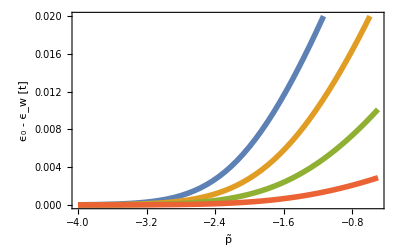

```mathematica
DispersionRSet2=Sqrt[2]tR Subscript[vSet2, perp]/lBSet2 ParabolicCylinderD[lBSet2^2/Subscript[vSet2, perp]^2(δϵ^2-Subscript[vSet2, parallel]^2 dPz^2)/2,Sqrt[2]py lBSet2]+(δϵ+Subscript[vSet2, parallel] dPz)ParabolicCylinderD[lBSet2^2/Subscript[vSet2, perp]^2(δϵ^2-Subscript[vSet2, parallel]^2 dPz^2)/2-1,Sqrt[2]py lBSet2]/.δϵ->ϵ-ϵ0R/.BBLSet2;
EnergyRSet2[tildePy_,tRvar_]:=ϵ-ϵ0R/.FindRoot[DispersionRSet2/.py->tildePy/(Sqrt[2]lBSet2)/.dPz->0/.tR->tRvar,{ϵ,ϵ0R/.BBLSet2}]/.BBLSet2
SetOptions[Plot,BaseStyle-> {FontSize-> 12,Thick}];
Plot[{EnergyRSet2[tildePy,-Tan[2.3/2]],EnergyRSet2[tildePy,-Tan[1.49/2]],EnergyRSet2[tildePy,-Tan[0.7/2]],EnergyRSet2[tildePy,-Tan[0.2/2]]},{tildePy,-4,-0.5},PlotStyle->{Thickness[0.01]},Frame->True,FrameLabel->{"p̃","ϵ_0 - ϵ_w [t]"}]
Export["~/Dropbox/Papers-Vadim/CME-long/figures/boundary-states-dispersion.eps",%];
```